```mathematica
data50=Import["/home/student/BEM/moon_pool_small_a0d75_T5d0_h80/result.json"];
data55=Import["/home/student/BEM/moon_pool_small_a0d75_T5d5_h80/result.json"];
data60=Import["/home/student/BEM/moon_pool_small_a0d75_T6d0_h80/result.json"];
data65=Import["/home/student/BEM/moon_pool_small_a0d75_T6d5_h80/result.json"];
data70=Import["/home/student/BEM/moon_pool_small_a0d75_T7d0_h80/result.json"];
data75=Import["/home/student/BEM/moon_pool_small_a0d75_T7d5_h80/result.json"];
data80=Import["/home/student/BEM/moon_pool_small_a0d75_T8d0_h80/result.json"];
data85=Import["/home/student/BEM/moon_pool_small_a0d75_T8d5_h80/result.json"];
data90=Import["/home/student/BEM/moon_pool_small_a0d75_T9d0_h80/result.json"];
data95=Import["/home/student/BEM/moon_pool_small_a0d75_T9d5_h80/result.json"];
data100=Import["/home/student/BEM/moon_pool_small_a0d75_T10d0_h80/result.json"];

fftPitch[data_]:=Module[{n},n=Length["time"/.data];Return[(2/n)*Abs@Fourier["floatingbody_pitch"/.data]];];
fftHeave[data_]:=Module[{n},n=Length["time"/.data];Return[(2/n)*Abs@Fourier[("floatingbody_COM"/.data)ᵀ[[3]]-75]];];
fftSurge[data_]:=Module[{n},n=Length["time"/.data];Return[(2/n)*Abs@Fourier[("floatingbody_COM"/.data)ᵀ[[1]]-200]];];
getPeriof[data_]:=Module[{n,dt},dt=0.2;n=Length["time"/.data];Return@Table[(i/(n*dt))^-1,{i,1,n,1}]];
getTime[data_]:=Module[{},Return[("time"/.data)];];
```

```mathematica
Do[data75[[i]][[2]]=data75[[i]][[2]][[;;547]],{i,1,Length[data75]}]
```

## Pitch

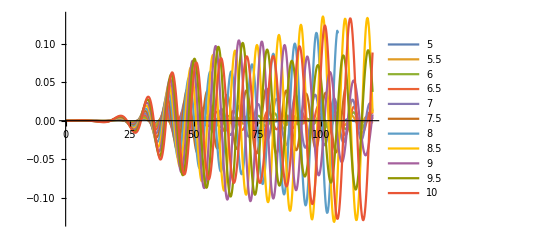

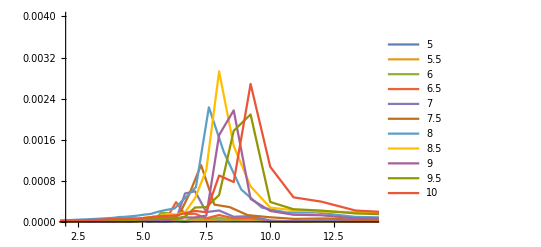

-Graphics3D-

```mathematica
ListPlot[Table[
Transpose[{"time"/.data,"floatingbody_pitch"/.data}]
,{data,{data50,data55,data60,data65,data70,data75,data80,data85,data90,data95,data100}}]
,Joined->True
,PlotRange->All
,PlotLegends->{5,5.5,6,6.5,7,7.5,8,8.5,9,9.5,10}
]

ListPlot[Table[
Transpose[{getPeriof[data],fftPitch[data]}]
,{data,{data50,data55,data60,data65,data70,data75,data80,data85,data90,data95,data100}}]
,Joined->True
,PlotRange->{{2,14},{0,4*10^-3}}
,PlotLegends->{5,5.5,6,6.5,7,7.5,8,8.5,9,9.5,10}
]

ListPlot3D[Flatten[
Table[
Transpose[{
getPeriof[data[[2]]],
Table[data[[1]],{i,1,Length[getPeriof[data[[2]]]]}],
fftPitch[data[[2]]]}]
,{data,{{5,data50},{5.5,data55},{6,data60},{6.5,data65},{7.,data70},{7.5,data75},{8.,data80},{8.5,data85},{9.,data90},{9.5,data95},{10.,data100}}}],1],
PlotRange->{{2,14},{5,10},{0,4*10^-3}},
AxesLabel->{"Period [s]","Incident [m]","FFT"},
TicksStyle->Black,
AxesStyle->Directive[{Black,FontSize->30,FontFamily->"Times"}],
ImageSize->400,
ColorFunction->"SouthwestColors"
]
```

## Surge

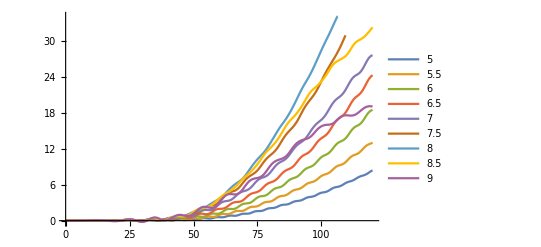

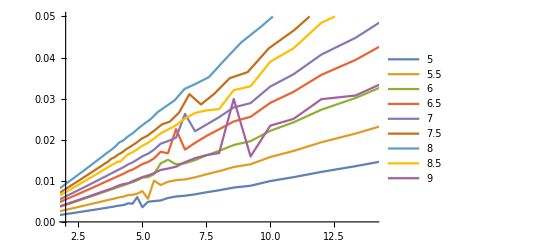

-Graphics3D-

```mathematica
ListPlot[Table[
Transpose[{getTime[data],("floatingbody_COM"/.data)ᵀ[[1]]-200}]
,{data,{data50,data55,data60,data65,data70,data75,data80,data85,data90}}]
,Joined->True
,PlotLegends->{5,5.5,6,6.5,7,7.5,8,8.5,9}
]

ListPlot[Table[
Transpose[{getPeriof[data],fftSurge[data]}]
,{data,{data50,data55,data60,data65,data70,data75,data80,data85,data90}}]
,Joined->True
,PlotRange->{{2,14},{0,5*10^-2}}
,PlotLegends->{5,5.5,6,6.5,7,7.5,8,8.5,9}
]

ListPlot3D[Flatten[
Table[
Transpose[{
getPeriof[data[[2]]],
Table[data[[1]],{i,1,Length[getPeriof[data[[2]]]]}],
fftSurge[data[[2]]]}]
,{data,{{5,data50},{5.5,data55},{6,data60},{6.5,data65},{7.,data70},{7.5,data75},{8.,data80},{8.5,data85},{9.,data90}}}],1],
PlotRange->{{2,14},{5,9},{0,4*10^-2}},
AxesLabel->{"Period [s]","Incident [m]","FFT"},
TicksStyle->Black,
AxesStyle->Directive[{Black,FontSize->15,FontFamily->"Times"}],
ImageSize->400,
ColorFunction->"SouthwestColors"
]
```

## Heave

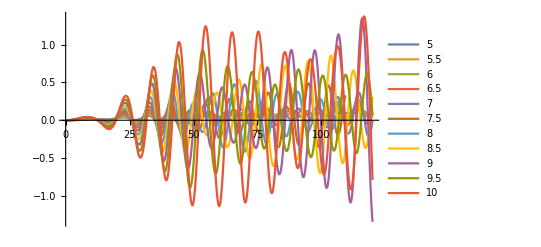

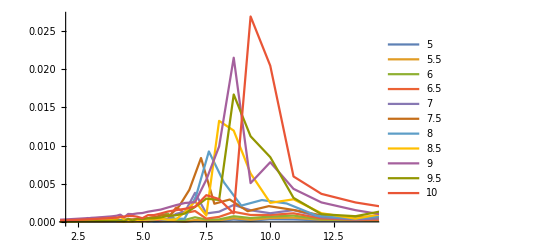

-Graphics3D-

```mathematica
ListPlot[Table[
Transpose[{getTime[data],("floatingbody_COM"/.data)ᵀ[[3]]-75}]
,{data,{data50,data55,data60,data65,data70,data75,data80,data85,data90,data95,data100}}]
,Joined->True
,PlotRange->All
,PlotLegends->{5,5.5,6,6.5,7,7.5,8,8.5,9,9.5,10}
]

ListPlot[Table[
Transpose[{getPeriof[data],fftHeave[data]}]
,{data,{data50,data55,data60,data65,data70,data75,data80,data85,data90,data95,data100}}]
,Joined->True
,PlotRange->{{2,14},All}
,PlotLegends->{5,5.5,6,6.5,7,7.5,8,8.5,9,9.5,10}
]

ListPlot3D[Flatten[
Table[
Transpose[{
getPeriof[data[[2]]],
Table[data[[1]],{i,1,Length[getPeriof[data[[2]]]]}],
fftHeave[data[[2]]]}]
,{data,{{5,data50},{5.5,data55},{6,data60},{6.5,data65},{7.,data70},{7.5,data75},{8.,data80},{8.5,data85},{9.,data90},{9.5,data95},{10.,data100}}}],1],
PlotRange->{{2,14},{5,10},All},
AxesLabel->{"Period [s]","Incident [m]","FFT"},
TicksStyle->Black,
AxesStyle->Directive[{Black,FontSize->15,FontFamily->"Times"}],
ImageSize->400,
ColorFunction->"SouthwestColors"
]
```